```mathematica
(* IMPORT MODULES *)
ClearAll[m1,m2,m3]
SetDirectory[NotebookDirectory[]];
NotebookEvaluate["modules/oscillator_bracket.nb"];
NotebookEvaluate["modules/mews_and_alphas.nb"];
NotebookEvaluate["modules/operators.nb"];
NotebookEvaluate["modules/hamiltonian.nb"];
NotebookEvaluate["modules/silvestre_parameters.nb"];
NotebookEvaluate["modules/golden_search.nb"];
On[Assert]
SetOptions[EvaluationNotebook[],StyleDefinitions->Notebook[{Cell[StyleData[StyleDefinitions->"Default.nb"]],Cell[StyleData["Graphics"],FontFamily->"Times"]},StyleDefinitions->"PrivateStylesheetFormatting.nb"]];
```

```mathematica
qns={{{"J","P","L","S","e"},{1/2,+1,0,1/2,0},{1/2,+1,1,1/2,0},{1/2,+1,1,3/2,0},{1/2,+1,2,3/2,0}},{{"J","P","L","S","e"},{3/2,+1,1,1/2,0},{3/2,+1,2,1/2,0},{3/2,+1,0,3/2,0},{3/2,+1,1,3/2,0},{3/2,+1,2,3/2,0},{3/2,+1,3,3/2,0}},{{"J","P","L","S","e"},{5/2,+1,2,1/2,0},{5/2,+1,3,1/2,0},{5/2,+1,1,3/2,0},{5/2,+1,2,3/2,0},{5/2,+1,3,3/2,0},{5/2,+1,4,3/2,0}},{{"J","P","L","S","e"},{7/2,+1,3,1/2,0},{7/2,+1,4,1/2,0},{7/2,+1,2,3/2,0},{7/2,+1,3,3/2,0},{7/2,+1,4,3/2,0},{7/2,+1,5,3/2,0}},{{"J","P","L","S","e"},{1/2,-1,1,1/2,0},{1/2,-1,1,3/2,0},{1/2,-1,2,3/2,0}},{{"J","P","L","S","e"},{3/2,-1,1,1/2,0},{3/2,-1,2,1/2,0},{3/2,-1,1,3/2,0},{3/2,-1,2,3/2,0},{3/2,-1,3,3/2,0}},{{"J","P","L","S","e"},{5/2,-1,2,1/2,0},{5/2,-1,3,1/2,0},{5/2,-1,1,3/2,0},{5/2,-1,2,3/2,0},{5/2,-1,3,3/2,0},{5/2,-1,4,3/2,0}},{{"J","P","L","S","e"},{7/2,-1,3,1/2,0},{7/2,-1,4,1/2,0},{7/2,-1,2,3/2,0},{7/2,-1,3,3/2,0},{7/2,-1,4,3/2,0},{7/2,-1,5,3/2,0}}};
```

```mathematica
For[iqn=1,iqn≤Length[qns],iqn++,

Print[iqn];
qn=qns[[iqn]];
whichBellow={};
startCondition=1;

While[Length[whichBellow]≠0+startCondition,
For[iBelow=1,iBelow≤Length[whichBellow],iBelow++,
pos=whichBellow[[iBelow]];
qn[[pos,5]]+=1
];
startCondition=0;
whichBellow={};

For[ep=2,ep≤Length[qn],ep++,
Print[ToString[ep]<>"/"<>ToString[Length[qn]]];
ClearAll[J,P,Isospin,γMax,Λ,m1,m2,m3,projector,project,size,firstNonZero,ham,sM,t1,t2];
(**** !!!TUNABLE PARAMETERS!!! ****)
J=qn[[ep,1]];(* Total angular momentum J = Λ + S *)
P=qn[[ep,2]];(* Parity P=(-1)^(Subscript[l, ρ]+Subscript[l, λ]) *)
Isospin=1;(* Isospin, 0 means flavour antisymmetric, 1 means symmetric *)
γMax=8;(* Maximum energy of considered basis states (2n+l+2N+L), use this to control Subscript[N, Q] *)
Λ=qn[[ep,3]];(* Total orbital angular momentum Λ = Subscript[l, ρ] + Subscript[l, λ] *)
S=qn[[ep,4]];(* Total spin *)
m1=sq;(* mass of quark 1 *)
m2=sq;(* mass of quark 2 *)
m3=bq;(* mass of quark 3 *)
excited=qn[[ep,5]];(* Choose excited state, 0 for ground state *)
groundMass=6.033;
save=True;(* Do you want to save parameters and mass to csv file? *)
(**** !!!END OF TUNABLE PARAMETERS!!! ****)
(* Choose to project depending if m1=m2 or m1≠m2, True and False, respectively *)
project=If[m1==m2,True,False];
(* Obtain projector matrix *)
projector=Projector[J,P,Λ,S,γMax,Isospin];
(* Calculate generalised transformation matrices *)
{t1time,t1}=AbsoluteTiming[tMatrix[J,P,Λ,S,γMax,m1,m2,m3,1]];
{t2time,t2}=AbsoluteTiming[tMatrix[J,P,Λ,S,γMax,m1,m2,m3,2]];
(* Obtain size of basis from size of talmi matrices (Subscript[N, Q]) *)
size=Dimensions[t1][[1]];
(* If projector has been applied, find position of first non-zero eigenvalue, if not applied then it's 1 *)
firstNonZero=If[project==True,size-Total[Diagonal[projector]]+excited+1,1+excited];
ham[ω_]:=Hb[J,P,Isospin,Λ,S,γMax,ω,m1,m2,m3,project];
sM=stateMatrix[J,P,Λ,S,γMax];
Print[sM//Length];
(* Find minimum and errors*)
{minTime,{a,b,data}}=AbsoluteTiming[goldenSearch[ham,firstNonZero,0.1,0.8,0.0005]];
wMin=(a+b)/2;
eigvalMin=Eigenvalues[ham[wMin]][[-firstNonZero]];
If[eigvalMin<groundMass+0.8,AppendTo[whichBellow,ep]];
Print["{ω_min,E_min}: ",{Around[wMin,a-wMin],eigvalMin}];
(* Save data *)
If[save,
dataset=Import["ladders.mx"];
quarkDict=Association[{uq->"u",sq->"s",cq->"c",bq->"b"}];
If[Isospin==0&&m1==uq&&m2==uq,secondQuark="d",secondQuark=quarkDict[m2]];
quarks=quarkDict[m1]<>secondQuark<>quarkDict[m3];
row={quarks,J,Λ,S,P,Isospin,excited,γMax,Round[wMin,0.0001],Round[eigvalMin,0.0001]};
If[MemberQ[dataset,row]==False,AppendTo[dataset,row];Export["ladders.mx",dataset];Print["Entry Added"],Print["Entry Already exists"]];
](* End of if *)
];(* End of ep for loop *)
Print[whichBellow]
](* End of While loop *)
];;(* End of iqn for loop *)
```

{{{0.,2.4546},{0.1,2.4546}},{{0.,3.0249},{0.1,3.0249}},{{0.,3.1136},{0.1,3.1136}},{{0.,3.1141},{0.1,3.1141}},{{0.,3.2034},{0.1,3.2034}},{{0.,3.2424},{0.1,3.2424}},{{0.,3.3102},{0.1,3.3102}},{{0.,3.4907},{0.1,3.4907}},{{0.,3.5441},{0.1,3.5441}},{{0.,3.6602},{0.1,3.6602}},{{0.,3.7883},{0.1,3.7883}},{{0.13,2.5349},{0.23,2.5349}},{{0.13,3.0686},{0.23,3.0686}},{{0.13,3.0929},{0.23,3.0929}},{{0.13,3.1136},{0.23,3.1136}},{{0.13,3.1643},{0.23,3.1643}},{{0.13,3.2034},{0.23,3.2034}},{{0.13,3.2758},{0.23,3.2758}},{{0.13,3.2782},{0.23,3.2782}},{{0.13,3.3102},{0.23,3.3102}},{{0.13,3.5158},{0.23,3.5158}},{{0.13,3.5301},{0.23,3.5301}},{{0.13,3.5441},{0.23,3.5441}},{{0.13,3.6602},{0.23,3.6602}},{{0.13,3.7883},{0.23,3.7883}},{{0.13,3.8258},{0.23,3.8258}},{{0.26,3.0929},{0.36,3.0929}},{{0.26,3.1136},{0.36,3.1136}},{{0.26,3.1643},{0.36,3.1643}},{{0.26,3.2782},{0.36,3.2782}},{{0.26,3.3102},{0.36,3.3102}},{{0.26,3.5301},{0.36,3.5301}},{{0.26,3.5441},{0.36,3.5441}},{{0.26,3.5934},{0.36,3.5934}},{{0.26,3.7035},{0.36,3.7035}},{{0.26,3.7883},{0.36,3.7883}},{{0.26,3.8258},{0.36,3.8258}},{{0.39,3.1136},{0.49,3.1136}},{{0.39,3.3102},{0.49,3.3102}},{{0.39,3.5441},{0.49,3.5441}},{{0.39,3.5891},{0.49,3.5891}},{{0.39,3.5934},{0.49,3.5934}},{{0.39,3.7035},{0.49,3.7035}},{{0.39,3.8258},{0.49,3.8258}},{{0.39,4.2647},{0.49,4.2647}},{{0.62,2.8016},{0.72,2.8016}},{{0.62,2.842},{0.72,2.842}},{{0.62,2.8857},{0.72,2.8857}},{{0.62,3.2888},{0.72,3.2888}},{{0.62,3.3141},{0.72,3.3141}},{{0.62,3.3786},{0.72,3.3786}},{{0.62,3.4295},{0.72,3.4295}},{{0.62,3.4556},{0.72,3.4556}},{{0.62,3.4973},{0.72,3.4973}},{{0.62,3.5925},{0.72,3.5925}},{{0.75,2.8016},{0.85,2.8016}},{{0.75,2.842},{0.85,2.842}},{{0.75,2.8857},{0.85,2.8857}},{{0.75,3.2888},{0.85,3.2888}},{{0.75,3.3141},{0.85,3.3141}},{{0.75,3.3625},{0.85,3.3625}},{{0.75,3.3786},{0.85,3.3786}},{{0.75,3.4295},{0.85,3.4295}},{{0.75,3.4556},{0.85,3.4556}},{{0.75,3.4647},{0.85,3.4647}},{{0.75,3.4973},{0.85,3.4973}},{{0.75,3.5508},{0.85,3.5508}},{{0.75,3.5925},{0.85,3.5925}},{{0.88,2.842},{0.98,2.842}},{{0.88,3.3141},{0.98,3.3141}},{{0.88,3.3529},{0.98,3.3529}},{{0.88,3.3625},{0.98,3.3625}},{{0.88,3.4241},{0.98,3.4241}},{{0.88,3.4647},{0.98,3.4647}},{{0.88,3.4973},{0.98,3.4973}},{{0.88,3.5218},{0.98,3.5218}},{{0.88,3.5508},{0.98,3.5508}},{{0.88,3.5925},{0.98,3.5925}},{{0.88,4.0528},{0.98,4.0528}},{{1.01,3.3529},{1.11,3.3529}},{{1.01,3.3625},{1.11,3.3625}},{{1.01,3.4241},{1.11,3.4241}},{{1.01,3.5218},{1.11,3.5218}},{{1.01,3.5508},{1.11,3.5508}},{{1.01,3.5925},{1.11,3.5925}},{{1.01,3.8172},{1.11,3.8172}},{{1.01,3.938},{1.11,3.938}},{{1.01,4.0528},{1.11,4.0528}}}

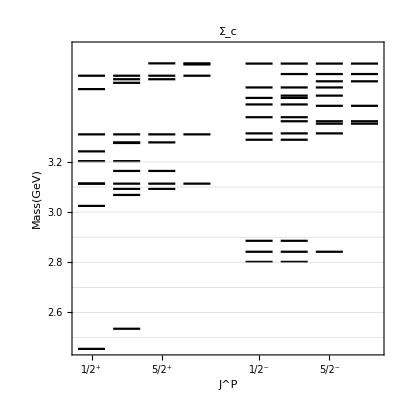

```mathematica
separation=0.13;
length=0.1;
split=0.1;
tower[baryon_,J_,P_,separation_,split_,lineLength_]:=Module[{dataset,list,pAssoc,start},
(* Import dataset of all masses *)
dataset=Import["ladders.mx"];
(* Make a selection of masses based on quantum numbers *)
list=Table[If[dataset[[i+1,1]]==baryon&&dataset[[i+1,8]]>4&&dataset[[i+1,2]]==J&&dataset[[i+1,5]]==P,dataset[[i+1,10]]],{i,1,Length[dataset]-1}];
(* Delete Null cases and sort masses*)
list = DeleteCases[list,Null]//Sort;
pAssoc=<|1->0,-1->4|>;
(* Given J and P determine position of tower *)
j=J-1/2+pAssoc[P];
s=If[P==-1,split,0];
start=j*separation+s;
(* From obtained masses, construct lines *)
lines=Table[{{start,list[[i]]},{start+lineLength,list[[i]]}},{i,1,Length[list]}]
]
mykeTowers[baryon_,separation_,split_,lineLength_]:=Module[{towers,js,ps,i,j,J,P,lines},
towers={};
js={1/2,3/2,5/2,7/2};
ps={1,-1};
For[i=1,i≤Length[ps],i++,
For[j=1,j≤Length[js],j++,
J=js[[j]];
P=ps[[i]];
lines=tower[baryon,J,P,separation,split,lineLength];
For[l=1,l≤Length[lines],l++,AppendTo[towers,lines[[l]]]]
](* End of j loop *)
](* End of i loop *);
Return[towers]
]
towers=mykeTowers["uuc",separation,split,length]
ground=towers[[1,1,2]];

fontSize=10;
tick1={0.05,Style["1/2^+",FontSize->fontSize,Black,Bold]};
tick2={0.05+separation,Style["3/2^+",FontSize->fontSize,Black,Bold]};
tick3={0.05+2*separation,Style["5/2^+",FontSize->fontSize,Black,Bold]};
tick4={0.05+3*separation,Style["7/2^+",FontSize->fontSize,Black,Bold]};
tick5={0.05+4*separation+split,Style["1/2^-",FontSize->fontSize,Black,Bold]};
tick6={0.05+5*separation+split,Style["3/2^-",FontSize->fontSize,Black,Bold]};
tick7={0.05+6*separation+split,Style["5/2^-",FontSize->fontSize,Black,Bold]};
tick8={0.05+7*separation+split,Style["7/2^-",FontSize->fontSize,Black,Bold]};

lowest=towers[[1,1,2]];
yMin=Ceiling[lowest,-0.1];
yMax=yMin+0.8;
ticks[min_,max_]:=Module[{d=FindDivisions[{min,max},6],n},n=Ceiling@Log10@Max@Denominator@d;{#,NumberForm[#,{∞,n}]}&/@N@d]
t=ticks[yMin,yMax];

frameTicks={{t,Automatic},{{tick1,tick2,tick3,tick4,tick5,tick6,tick7,tick8},None}};

plot=ListPlot[towers,
Joined->True,
PlotRange->{{0,0.05+7*separation+split+0.05},{lowest,lowest+1.2}},
PlotStyle->{Black},
Frame->{{True,True},{True,False}},
FrameTicks->frameTicks,
GridLines->{None,Table[x,{x,yMin,yMax,0.1}](*Table[ground+0.1*x,{x,0,10}]*)},
GridLinesStyle->{LightGray,Dashed},
FrameLabel->{Style["J^P",FontSize->12],Style["Mass(GeV)",FontSize->12]},
PlotLabel->Style["Σ_c",FontSize->16,FontFamily->"Times",Black],
AspectRatio->1.05]
```

```mathematica
Export["plots/Silvestre/towers/usb.pdf",plot,"PDF","AllowRasterization"->False]
```

plots/Silvestre/towers/usb.pdf